```mathematica
(*Data*)
μ=3.9877848 10^14;
Mp=1000;
l=50000;
Mt =1000;
Nn = 20;
rc=6870000;
τ = 20000000;

ranget = 30000;



psiQ =τ 

(*Position vectorc and linear kinetic energy (translation of centre of mass)*)
rm[t] = ({{rc Cos[θ[t]]}, {rc Sin[θ[t]]}, {0}});
rp1[t]=rm[t]+({{l Cos[α[t]] Cos[ψ[t]+θ[t]]}, {l Cos[α[t]] Sin[ψ[t]+θ[t]]}, {l Sin[α[t]]}});
rp2[t]=rm[t]-({{l Cos[α[t]] Cos[ψ[t]+θ[t]]}, {l Cos[α[t]] Sin[ψ[t]+θ[t]]}, {l Sin[α[t]]}});

rm'[t]=D[rm[t], t];
rp1'[t]=D[rp1[t], t];
rp2'[t]=D[rp2[t], t];

Subscript[T, lin]=1/2 (2*Mp) (Transpose[rm'[t]].rm'[t]);

(*Rotational kinetic energy (rotation of system about centre of mass)*)
ω[t]=({{0}, {-Cos[γ[t]] α'[t]+Cos[α[t]] Sin[γ[t]] (θ'[t]+ψ'[t])}, {Sin[γ[t]] α'[t]+Cos[α[t]] Cos[γ[t]] (θ'[t]+ψ'[t])}});

ⅈp=({{0, 0, 0}, {0, 2 Mp l^2, 0}, {0, 0, 2 Mp l^2}})  ;
ⅈtether=If[OddQ[Nn],
(*odd number of points, sum of moments of pairs of point masses at ±nδl from centre*)
Sum[({{0, 0, 0}, {0, 2 Mt/Nn ((n l)/(Nn+1))^2, 0}, {0, 0, 2 Mt/Nn ((n l)/(Nn+1))^2}}),{n,1,(Nn-1)/2}],
(*even number of points, sum of moments of pairs of point masses at ±(2n-1)/2 δl from centre, (1/2,3/2,5/2...)*)
Sum[({{0, 0, 0}, {0, 2 Mt/Nn (((2n-1) l)/(2(Nn+1)))^2, 0}, {0, 0, 2 Mt/Nn (((2n-1) l)/(2(Nn+1)))^2}}),{n,1,Nn/2}]];
Subscript[ⅈ, 123] = ⅈp+ⅈtether;

Subscript[T, rot]=1/2 Transpose[ω[t]].Subscript[ⅈ, 123].ω[t];

T=Subscript[T, lin]+Subscript[T, rot];

(*potential energy*)
Up1=-(μ Mp)/(√(Transpose[rp1[t]].rp1[t]));
Up2=-(μ Mp)/(√(Transpose[rp2[t]].rp2[t]));
Utether=If[OddQ[Nn],
(*sum of potentials for odd number of points (sum from 0 first to get center mass)
position vector is r(centre) + vector in direction from centre to payload, with magnitude length/number of points+1 *)
Sum[(-(μ Mt/Nn)/(√(Transpose[rm[t]+n*rt[t]].(rm[t]+n*rt[t])))),{n,0,(Nn-1)/2}]+Sum[(-(μ Mt/Nn)/(√(Transpose[rm[t]-n*rt[t]].(rm[t]-n*rt[t])))),{n,1,(Nn-1)/2}],
(*sum of potentials for even number of points, same idea but vector is 1/2, 3/2, 5/2 * length/Nn+1 due to symmetry around center *)
Sum[(-(μ Mt/Nn)/(√(Transpose[rm[t]+(2n-1)/2*rt[t]].(rm[t]+(2n-1)/2*rt[t])))),{n,1,Nn/2}]+Sum[(-(μ Mt/Nn)/(√(Transpose[rm[t]-(2n-1)/2*rt[t]].(rm[t]-(2n-1)/2*rt[t])))),{n,1,Nn/2}]];
V = Up1+Up2+Utether;
θ[t]= √(μ/rc^3)t;
θ'[t]= √(μ/rc^3);
θ''[t]=0;
L=T-V;
eqn1=Simplify[D[D[T, ψ'[t]], t]-D[T, ψ[t]]]+ D[V, ψ[t]]-psiQ;
eqn2=Simplify[D[D[T, α'[t]], t]-D[T, α[t]]]+ D[V, α[t]];
```

20000000

```mathematica
(*initial conditions*)
alpha0 = 0;
alphadsh0 = 0;
psi0 = 0.5;
psidsh0 =0;


system=NDSolve[{eqn1[[1]][[1]]==0,eqn2[[1]][[1]]==0,α[0]==alpha0,α'[0]==alphadsh0,ψ[0]==psi0,ψ'[0]==psidsh0},{ψ,α},{t,0,ranget},MaxSteps->∞,AccuracyGoal->Automatic,PrecisionGoal->Automatic,Method->{"EquationSimplification"->"Residual"}];
```

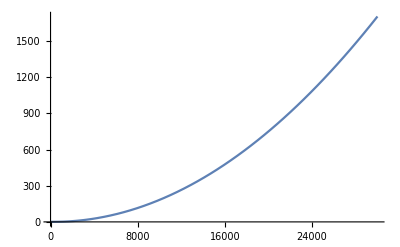

```mathematica
gammas[t_]:=γ[t]/.system[[1]];
alphas[t_]:=α[t]/.system[[1]];
psis[t_]:=ψ[t]/.system[[1]];
gammadshs[t_]:=Evaluate[γ'[t]/.system[[1]]];
thetadshs[t_]:=Evaluate[θ'[t]/.system[[1]]];
alphadshs[t_]:=Evaluate[α'[t]/.system[[1]]];
psidshs[t_]:=Evaluate[ψ'[t]/.system[[1]]];
Plot[psis[t],{t,0,ranget}]
```